Corso di Laboratorio Computazionale, Corso di Laurea in Matematica,  Università di Padova.        
A.A. 2021-2022

# Esercizi 3: Frattali classici

Notebook del gruppo:

Componenti del gruppo:

Se ci sono state collaborazioni e/o aiuti al di fuori del gruppo, dichiararli:
In collaborazione con: 
Aiutato da:

Consegna entro:  ...

```mathematica
SetOptions[EvaluationNotebook[],Background->LightCyan]
```

## Esercizio 3.1: Guarnizione di Sierpinski

## Testo dell’esercizio

### Testo dell’esercizio

Esercizio 3.1

1) Disegnare le approssimazioni della guarnizione di Sierpinski, illustrata nella seguente figura:

2) Mettere in evidenza la autosimilarità

#### Suggerimenti ed osservazioni:

- Lavorare su liste di triangoli, con triangolo=lista dei suoi tre vertici.
- La funzione da iterare rende un triangolo e ne restituisce 3. Basta scrivere i vertici di questi 3 triangoli in funzione dei vertici di quello iniziale.
- La primitiva grafica “triangolo pieno” si chiama   Polygon[{vertici}]

Per evidenziare la autosimilarità utilizzare una finestrella ed opportuni ingradimenti di opportune parti.

## Soluzione

In questo esercizio rappresentiamo il triangolo di Sierpinski.

Per costruire il triangolo di Sierpinski alla n-esima itezione ( il frattale sarebbe rappresentato dal limite all’infinito di queste iterazioni ) bisogna applicare n volte una funzione che da un originario triangolo equilatero ne ricavi tre, unendo i punti medi di ogni lato del triangolo originale.

Definiamo innanzitutto la figura di partenza, il triangolo equilatero.
Costruiamo una funzione triangolo che dato il lato  restituisce i vertici di un triangolo equilatero situato nel primo quadrante con base sull’asse x e il vertice più a sinistra centrato nell’origine.

```mathematica
triangolo[lato_]:= {{0.,0.},{lato,0.},{lato*0.5,√3*0.5 lato}}
```

```mathematica
tr=triangolo[1]
```

{{0.,0.},{1,0.},{0.5,0.866025}}

Definiamo una funzione che data una lista di vertici di un triangolo equilatero mi restituisce una lista di vertici di 3 triangoli equilateri, utilizzando i vertici e i punti medi del triangolo originario.
Infatti, se traccio i segmenti che uniscono i punti medi del triangolo equilatero originale, divido la figura iniziale in 4 triangoli equilateri.
Qui sotto prendiamo i vertici di tutti i triangoli in cui si è divisa la figura a parte quello centrale.

```mathematica
Sierpinski1[tri_]:= {{tri[[1]],(tri[[1]]+tri[[2]])*0.5,(tri[[1]]+tri[[3]])*0.5},{tri[[2]],(tri[[2]]+tri[[3]])*0.5,(tri[[2]]+tri[[1]])*0.5},{tri[[3]],(tri[[3]]+tri[[2]])*0.5,(tri[[3]]+tri[[1]])*0.5}}
```

Mappiamo la funzione ad una lista di triangoli equilateri ed eseguiamo poi un Flatten[lista, 1] per evitare che si formino parentesi aggiuntive (e che quindi poi riapplicando la funzione non otterremmo il risultato desiderato).
Utilizziamo quindi  { tr } (come lista iniziale ), poichè questa funzione agisce su una lista di triangoli.

```mathematica
Sierpinski2[listatr_]:= Flatten[Map[Sierpinski1[#] &,listatr],1]
```

```mathematica
Sierpinski2[{tr}]
```

{{{0.,0.},{0.5,0.},{0.25,0.433013}},{{1,0.},{0.75,0.433013},{0.5,0.}},{{0.5,0.866025},{0.75,0.433013},{0.25,0.433013}}}

Ora usiamo la funzione Nest[funzione, punto iniziale, n] che applica itarativamente n volte la funzione  al punto iniziale.

```mathematica
Sierpinski3[n_,tr_]:=Nest[Sierpinski2,tr,n]
```

```mathematica
Sierpinski3[3,{tr}]
```

{{{0.,0.},{0.125,0.},{0.0625,0.108253}},{{0.25,0.},{0.1875,0.108253},{0.125,0.}},{{0.125,0.216506},{0.1875,0.108253},{0.0625,0.108253}},{{0.5,0.},{0.4375,0.108253},{0.375,0.}},{{0.375,0.216506},{0.3125,0.108253},{0.4375,0.108253}},{{0.25,0.},{0.3125,0.108253},{0.375,0.}},{{0.25,0.433013},{0.3125,0.32476},{0.1875,0.32476}},{{0.375,0.216506},{0.25,0.216506},{0.3125,0.32476}},{{0.125,0.216506},{0.25,0.216506},{0.1875,0.32476}},{{1,0.},{0.9375,0.108253},{0.875,0.}},{{0.875,0.216506},{0.8125,0.108253},{0.9375,0.108253}},{{0.75,0.},{0.8125,0.108253},{0.875,0.}},{{0.75,0.433013},{0.6875,0.32476},{0.8125,0.32476}},{{0.625,0.216506},{0.75,0.216506},{0.6875,0.32476}},{{0.875,0.216506},{0.75,0.216506},{0.8125,0.32476}},{{0.5,0.},{0.5625,0.108253},{0.625,0.}},{{0.625,0.216506},{0.6875,0.108253},{0.5625,0.108253}},{{0.75,0.},{0.6875,0.108253},{0.625,0.}},{{0.5,0.866025},{0.5625,0.757772},{0.4375,0.757772}},{{0.625,0.649519},{0.5,0.649519},{0.5625,0.757772}},{{0.375,0.649519},{0.5,0.649519},{0.4375,0.757772}},{{0.75,0.433013},{0.625,0.433013},{0.6875,0.541266}},{{0.5,0.433013},{0.5625,0.541266},{0.625,0.433013}},{{0.625,0.649519},{0.5625,0.541266},{0.6875,0.541266}},{{0.25,0.433013},{0.375,0.433013},{0.3125,0.541266}},{{0.5,0.433013},{0.4375,0.541266},{0.375,0.433013}},{{0.375,0.649519},{0.4375,0.541266},{0.3125,0.541266}}}

Rappresentiamo ora le liste di triangoli ottenute nel piano con la funzione Polygon[{vertici}] (che mi rappresenta una figura piena)

```mathematica
Sierpinski[n_,tr_]:= Graphics[{RGBColor[0.93,0.39,1.],Polygon[Sierpinski3[n,tr]]},AspectRatio->Automatic]
```

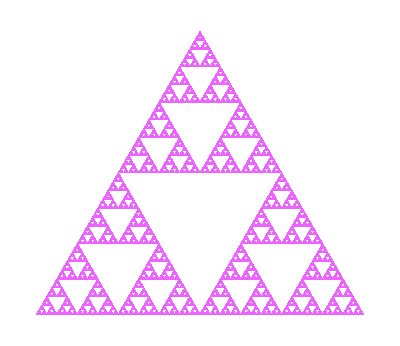

```mathematica
Sierpinski[6,{tr}]
```

Rappresentiamo le appprossimazioni del triangolo di Sierpinski in un’unica griglia con GraphicsGrid.
In questo caso vogliamo utilizzare NestList[funzione, punto iniziale, n] che mi riporta i risultati via via ottenuti in ogni iterazione, questo per evitare che ogni volta ricalcoli l’approssimazione di ordine n iterando dal punto iniziale.
Quindi, a differenza di prima, modifichiamo leggermente Sierpinski3 con NestList[...] creando una lista dei vertici delle approssimazioni fino a quella di ordine n .
Creiamo poi una lista di grafici (per rappresentarle tutte in una griglia) di ciascuna delle approssimazioni, la funzione utilizzata per creare la figura è identica a quella precedente ma sarà applicata ad un solo elemento della lsta di approssimazioni.
Poichè vogliamo creare una griglia che rappresenti 3 grafici in ognuna delle righe, vogliamo che la lista di grafici abbia lunghezza multiplo di 3.
Per fare ciò completiamo eventualmente la lista di grafici con dei grafici vuoti.
Dividiamo poi la lista di grafici in sottoliste di tre elementi e rappresentiamole in una griglia.

```mathematica
approssimazioni[n_,tr_]:=NestList[Sierpinski2,tr ,n ]
```

```mathematica
grafici1[n_,tr_]:= Table[ Graphics[{RGBColor[0.93,0.39,1.],Polygon[approssimazioni[n,tr][[t]]]},AspectRatio->Automatic,PlotLabel->"n = "<>ToString[t-1]],{t,1,n+1}]
```

```mathematica
grafici[n_,tr_]:= Join[grafici1[n,tr],Table[Graphics[],{t,n+2,Ceiling[(n+1)/3]*3}]]
```

```mathematica
griglia[n_,tr_]:=GraphicsGrid[Table[Table[ grafici[n,tr][[s+t]],{t,0,2}],{s,1,Ceiling[(n+1)/3]*3,3}],ImageSize-> Full]
```

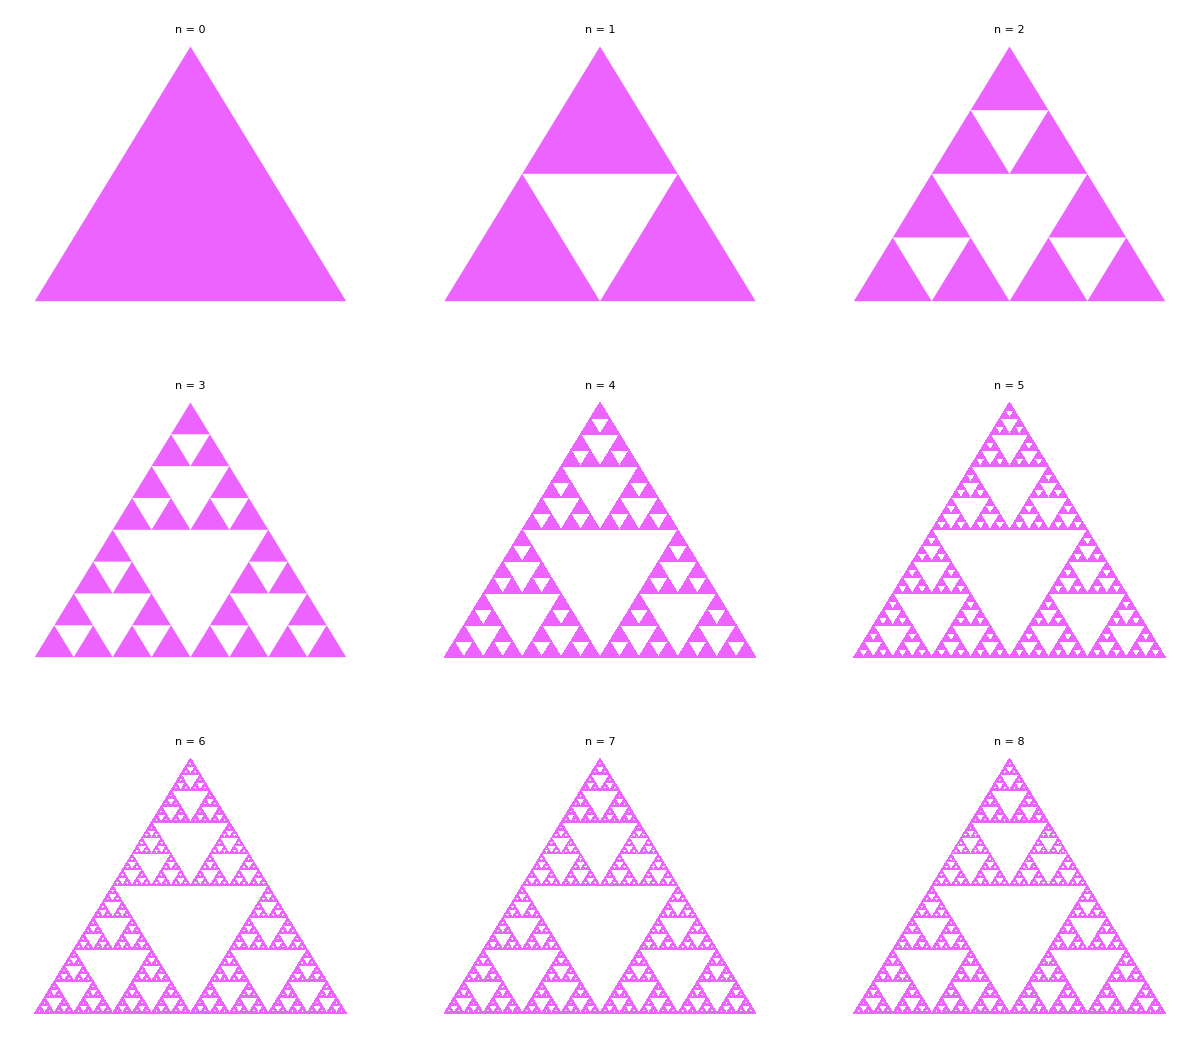

```mathematica
griglia[8,{tr}]
```

Notiamo la struttura autosimilare della struttura prodotta nella prima iterazione dell’algoritmo che approssima il triangolo di Sierpinski.
Con struttura autosimilare si intende una “figura” che è alla base di tutte le approssimazioni create. Infatti ognuna di queste puo’ essere costruita con unioni di   opportunamente riscalate.
Si vede che il numero di tali strutture si triplica ad ogni iterazione e la loro grandezza diminuisce di un fattore   1/2  (è (3,2) autosimilare, quindi ha dimensione di Hausdorff  ln[3]/ln[2] ).
Mettiamo in evidenza tale autosimilarità con oppurtune finestrelle.

Mostriamo, ad esempio, che tale struttura si ripete nel vertice in basso a sinistra delle approssimazioni di Sierpinski che abbiamo costruito.
Costruiamo allora una griglia n×2 che mostri a sinistra il riquadro della struttura ripetuta e a destra un suo ingrandimento.
Per fare ciò utilizziamo grafici1b[....] che mi crea la lista dei grafici delle approssimazioni da quella di ordine 2 fino all’ordine n con una finestra in basso a sinistra (unica differenza rispetto alla funzione che avevamo già definito in precedenza ) che riquadra la struttura di base.
Il riquadro rimpicciolisce di un fattore 1/2   i  suoi vertici ad  ogni iterazione come appunto fa la struttura ( il triangolo di Sierpinski è (3,2) autosimilare ).
Definiamo poi la lista di ingrandimenti. Rispetto alla lista che creeremo con la funzione sopra  viene cambiato il PlotRange sempre rispetto alle dimensione dell’altezza e della base della finestrella che abbiamo creato.
Infine creiamo una griglia per confrontare la struttura nel riquadro di ciascuna figura. Combiniamo quindi, in ordine, gli elementi di entrambe le liste, costruite con le funzioni definite sopra.

```mathematica
grafici1b[n_,tr_]:= Table[ Graphics[{RGBColor[0.93,0.39,1.],Polygon[approssimazioni[n,tr][[t]]],Green,Thickness[0.005],Line[{{0,0},{0,√3*0.5*0.5^(t-2)},{0.5^(t-2),√3*0.5*0.5^(t-2)},{0.5^(t-2),0},{0,0}}]},AspectRatio->Automatic,PlotLabel->"n = "<>ToString[t-1]],{t,3,n+1}]
```

```mathematica
grafici1c[n_,tr_]:= Table[ Graphics[{RGBColor[0.93,0.39,1.],Polygon[approssimazioni[n,tr][[t]]]},AspectRatio->Automatic,PlotLabel->"n = "<>ToString[t-1],PlotRange->{{0,0.5^(t-2)},{0,√3*0.5*0.5^(t-2)}}],{t,3,n+1}]
```

```mathematica
griglia2[n_,tr_]:=GraphicsGrid[Table[{grafici1b[n,tr][[t]],grafici1c[n,tr][[t]]},{t,1,n-1}], ImageSize->Full]
```

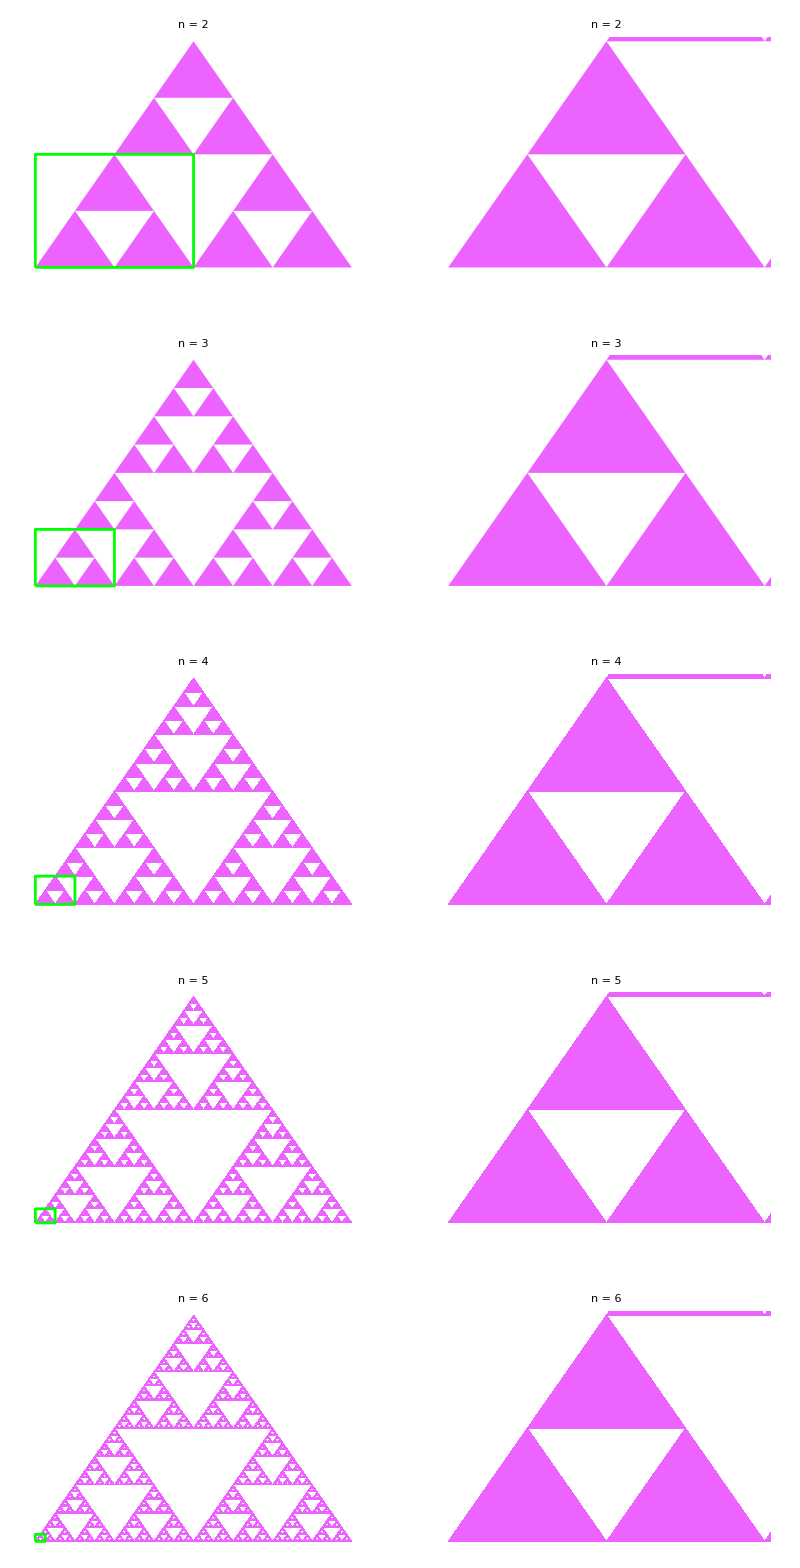

```mathematica
griglia2[6,{tr}]
```

Notiamo che la struttura riquadrata, opportunamente ingrandita, è sempre la stessa.
Mostriamo anche con un’animazione ( con ListAnimate[....] ) che ognuna delle approssimazioni precedenti si sovrappone al disegno finale di una approssimazione di Sierpinski di ordine maggiore.
Per fare ciò creiamo una tabella, i cui elementi verranno animati con ListAnimate[...], che, come prima, rappresenta gli elementi della lista di approssimazioni ma ognuno oppurtunamente riscalato.
Sappiamo che ad ogni iterazione la grandezza di ognuna delle componenti del triangolo diminuisce di un fattore 0.5, perciò rimpiccioliamo di 0.5 ^ (ordine di approssiamazione maggiore - ordine di approssimazione della figura nella lista ).

```mathematica
animazione[n_,tr_]:=ListAnimate[Table[ Graphics[{RGBColor[0.93,0.39,1.],Polygon[approssimazioni[n,tr][[t]]*(0.5)^(n+1-t)]},PlotRange->{{0,1},{0,0.5*√3}}],{t,2,n+1,1}],0.5]
```

```mathematica
animazione[7,{tr}]
```

## Esercizio 3.2: Tappeto di Sierpinski

## Testo dell’esercizio

### Testo dell’esercizio

Esercizio 3.2 Disegnare le approssimazioni del Sierpinski carpet, illustrato nella seguente figura:


egnare le approssimazioni del tappeto di Sierpinski

#### Suggerimenti ed osservazioni:

Suggerimenti:
- lavorare su liste di quadrati, con quadrati = lista dei suoi 4 vertici.
- La funzione da iterare prende un quadrato e ne restituisce 8. Conviene farla così:
     - si fa una Table (automaticamente, con il comando Table) che crea i 9 quadrati ottenuti dividendo i lati del quadrato in tre:
                        Table[{p1+m e1+n e2,.....},{m,0,2},{n,0,2}],
       ove e1 ed e2 sono i vettori della base standard di R^2.
     - si butta via quello centrale (Delete[lista, {posizione}])
- La primitiva grafica “quadrato pieno” si chiama   Polygon[{vertici}]

PS: Non creare la lista degli otto quadrati a mano: il codice è illeggibile, e non è generalizzabile alla spugna di Menger.

## Soluzione

In questo esercizio dobbiamo disegnare il tappeto di Sierpinski

Definiamo i quattro vertici del quadrato iniziale, che sarà un quadrato unità, come valori di una funzione chiamata QuadratoIniziale.

```mathematica
QuadratoIniziale:={{0,0},{0,1},{1,1},{1,0}}
```

Definiamo i seguenti vettori di ℝ^2:
 Sia un quadrato dato come lista dei suoi 4 vertici, consideriamo i suoi due vertici che si trovano nella diagonale y=x, chiamamoli vertice superiore (che si trova nella posizione 3 della lista) e vertice inferiore (che si trova nella posizione 1 della lista).

Per definire la funzione fe1, che mi dà un vettore nell’ asse OX (quindi ha seconda coordinata nulla) prendiamo la coordinata x del vertice superiore e le sottraiamo la coordinata x del vertice inferiore, e dividiamo per 3, per dividere ogni lato del quadrato iniziale in tre pezzi.

 Per definire la funzione fe2, che è un vettore nell’ asse OY (quindi ha prima coordinata nulla) prendiamo la coordinata y del vertice superiore e le sottraiamo la coordinata y del vertice inferiore, e dividiamo per 3.

Con la coordinata x  intendiamo la prima coordinata del vertice, e con y  la seconda.

```mathematica
fe1[lst_]:={(lst[[3]][[1]]-lst[[1]][[1]])/3,0};
fe2[lst_]:={0,(lst[[3]][[2]]-lst[[1]][[2]])/3};
```

Adesso definiamo la funzione che abbiamo chiamato tappeto1: dato un quadrato, che verrà dato come una lista dei suoi  4 vertici,  restituisce 9 quadrati.

Questa funzione riceve come parametro un quadrato. 

Facendo  Table, m e n prendono 3 valori differenti: da 0 a 2, cioè in totale abbiamo 9 combinazioni possibili in funzione dei valori di m e n, per questo otteniamo 9 quadrati differenti.

Al vertice che avevamo chiamato vertice inferiore  ( vi ) del quadrato passato come parametr, facciamo le seguenti operazioni per ottenere un quadrato più picccolo di lato  (Lunghezza lato Quadrato Iniziale)/3
I vertici di ogni quadrato creato si definiscono così:
⊳ Il vertice inferiore sinistro del nuovo quadrato è la prima coordinata, definita così:  vi + m·fe1[V] + n·fe2[V], con fe1 e fe2 definiti prima.
⊳ La seconda coordinata corrisponde al suo vertice superiore sinistro. Quindi, deve avere la stessa coordinata x che ha il vertice inferiore sinistro ed alla coordinata y vi aggiungiamo un’unità.
⊳ La terza coordinata è il suo vertice superiore destro. Quindi vi aggiungiamo un’unità alla coordinata x e alla coordinata y di vi.
⊳ La quarta coordinata è il suo vertice inferiore destro. Deve avere la stessa coordinata y che ha il vertice inferiore sinistro ed alla coordinata x vi aggiungiamo un’unità.

Inoltre facciamo un Flatten[....,1]  perché altrimenti otteniamo tre liste di tre quadrati ciascuna invece di una lista di 9 quadrati che è quello che vogliamo che restituisca per poi poter eliminare quello centrale con la seguente funzione tappeto2.

Dovuto a come abbiamo definito i vettori fe1 e fe2, la lunghezza dei lati di ognuno di questi 9 quadrati restituiti è uguale a =(Lunghezza lati Quadrato Iniziale)/3

```mathematica
tappeto1[V_]:=Flatten[Table[{V[[1]]+m fe1[V]+n fe2[V],V[[1]]+m fe1[V]+(n+1) fe2[V],V[[1]]+(m+1) fe1[V]+(n+1) fe2[V],V[[1]]+(m+1)fe1[V]+n fe2[V] },{m,0,2},{n,0,2}],1]
```

Adesso definiamo la seguente funzione che elimina il quadrato centrale dei 9 quadrati creati prima.
La seguente funzione, tappeto2, dato un quadrato come parametro, calcola tappeto1 del quadrato e elimina il quadrato nella posizione centrale, che si trova sempre nella posizione 5. 
Possiamo fare quest’operazione grazie alla funzione già implementata in Mathematica Delete

```mathematica
tappeto2[V_]:=Delete[tappeto1[V],5]
```

Quindi tappeto2 restituisce una lista di 8 quadrati: tutti meno quello centrale.

Qui di seguito definiamo la funzione tappeto3 che data una lista di quadrati fa una mappa sulla funzione tappeto2 (usando il comando /@ equivalente a Map).
Inotre facciamo un Flatten di profondità 1 perché c'è una proliferazione di parentesi.
È inevitabile poichè la funzione tappeto2 agisce su liste di quattro punti nel piano, non su liste di liste di quattro punti. 
Dunque la funzione tappeto2 mappata aggiunge un livello, che bisogna "sciogliere" con un Flatten di livello 1. Di questa forma la seguente funzione, tappeto4 , dà come output una lista di quadrati (invece di una lista di liste di quadrati) che si potranno disegnare alla fine con l’ultimo comando di questo esercizio, che dopo spiegheremo.

```mathematica
tappeto3[lista_]:=Flatten[tappeto2/@lista,1]
```

Adesso facciamo un Nest[ funzione, puntoIniziale, numeroIterazioni ].
Diamo come parametri iniziali: la funzione da iterare tappeto3, il quadrato iniziale e il numero di iterazioni che vorremo fare n.
E’ importante notare che mettiamo il quadrato iniziale tra parentesi perché la funzione tappeto3 riceve come parametro una lista di quadrati.

```mathematica
tappeto4[n_]:= Nest[ tappeto3 , {QuadratoIniziale} ,n]
```

Il seguente passo è disegnare in una griglia tappeto4 (a diverso numero di iterazioni).
Usiamo la funzione GraphicsGrid che genera una griglia grafica bidimensionale in cui gli sono disposti elementi bidimensionali (poligoni).
Per disegnare le successive iterazioni sullo stesso quadrato iniziale facciamo una Table che illustra le prime 4 iterazioni.
Allo stesso tempo, per ogni iterazione n, disegniamo con il comando Graphics i quadrati che restituisce la funzione tappeto4.
Per disegnare un quadrato con quatro vertici usiamo la funzione già implementata in Mathematica Polygon, che richiede come parametri una lista di quadrati (liste di 4 punti nel piano), quelli che restituisce la funzione tappeto4.

Per ragioni estetiche, scegliamo come dimensione del disegno quella più grande (Large)

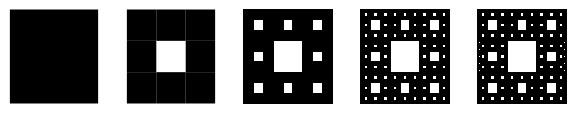

```mathematica
GraphicsGrid[{Table[Graphics@Polygon[tappeto4[n]],{n,0,4}]},ImageSize->Large]
```

## Esercizio 3.3: Spugna di Menger

## Testo dell’esercizio

### Testo dell’esercizio

Disegnare le approssimazioni della spugna di Menger mostrata nella seguente figura:

### Suggerimenti ed osservazioni:

Suggerimenti:
- procedere come nel caso precedente.
- La primitiva grafica è ora “cuboid”; naturalmente serve Graphics3D, non Graphics.

- Attenzione: i file sono piuttosto grossi e il rendering lento già per n=4. Salvare il notebook prima di fare le figure.

C’è anche un’altra possibile implementazione, che crea tables più piccole, ma non si guadagna in velocità:  ’idea è di lavorare solo con il vertice in basso a sinistra e con il lato del quadrato, invece che con tutti e quattro i vertici

## Soluzione

In questo esercizio disegneremo le approssimazioni della spugna di Menger

Innanzitutto definiamo il cubo iniziale unitario, con cui lavoreremo. Usiamo la funzione Cuboid:
Cuboid[pmin,pmax]: represents an axis-aligned filled cuboid with lower corner pmin and upper corner pmax.

```mathematica
CuboIniziale=Cuboid[{0,0,0},{1,1,1}];
```

Procediamo come nell’esecizio precedente.
Questa volta, siccome stiamo lavorando in ℝ^3, definiamo i seguenti vettori:
Il primo (rispettivamente secondo, terzo) vettore si trova nel asse OX (risp. OY, OZ) e prende la coordinata x (risp. y, z) del punto del cubo nel vertice superiore e le sottrae la coordinata x (risp. y, z) del punto del cubo nel vertice inferiore.

Eliminiamo dalla memoria del kernel le funzioni fe1 ed fe2 perché le abbiamo usate nell’ esercizio precedente

```mathematica
Clear[fe1];
Clear[fe2];
```

```mathematica
fe1[V_]:={(V[[2]][[1]]-V[[1]][[1]])/3,0,0};
fe2[V_]:={0,(V[[2]][[2]]-V[[1]][[2]])/3,0};
fe3[V_]:={0,0,(V[[2]][[3]]-V[[1]][[3]])/3};
```

Adesso definiamo la funzione cubo1 che riceve come parametro un cubo.
Della stessa forma che dell’ esercizio precedente dove m e n prendono 3 valori differenti: da 0 a 2. Abbiamo, però, aggiunto una variabile in più l, che va da 0 a 2 ( poichè siamo passati al caso tridimensionale ). In totale abbiamo 27 combinazioni possibili in funzione dei valori di m, n e l , per questo otteniamo 27 quadrati differenti a partire dal cubo passato come parametro.

Siccome Cuboid ha bisogno soltanto di due punti nello spazio, facciamo una Table con due coordinate, che rappresentano rispettivamente il punto nel vertice inferiore e superiore.

Ogni vertice inferiore dei 27 nuovi cubi, lo creiamo facendo: vertice inferiore + m·fe1[V] + n·fe2[V] + l·fe3[V], dove m,n e l prendono differenti valori.
Un’ altra osservazione: per creare il punto nel vertice superiore, siccome è il punto opposto al vertice inferiore dobbiamo aggiungere un’unità alla coordinata x, alla coordinata y e alla coordinata z.

Inoltre faciamo un Flatten di livello 2 perché altrimenti otteniamo una lista di 3 liste di 3 liste di 3 cubi invece di avere una sola lista con 27 cubi.
(Quando scrivo cubi mi referisco ai due vertici che definiscono un cubo insieme al comando Cuboid)

```mathematica
cubo1[V_]:=Flatten[Table[{V[[1]]+m fe1[V]+n fe2[V]+l fe3[V],V[[1]]+(m+1) fe1[V]+(n+1) fe2[V]+ (l+1) fe3[V]},{m,0,2},{n,0,2}, {l,0,2}],2]
```

Qualle cubi dobiamo eliminare? Quelli che si trovamo nelle posizioni 5, 11, 13, 14, 15, 17, 23 della lista di 27 cubi creata nel passo precedente.
Usiamo la funzione già implementata in mathematica Delete. Osserviamo che siccome dobbiamo eliminare più di un cubo, mettiamo i numeri di cubi da eliminare tra parentesi.

```mathematica
cubo2[V_]:=Delete[cubo1[V],{{5},{11},{13},{14},{15},{17},{23}}]
```

cubo3 riceve come parametro una lista di cubi. 
Inoltre, faciamo un Flatten di livello 1 perché c’è una proliferazione di parentesi, dovuto al fatto che la funzione cubo2 mappata aggiunge un livello, che bisogna “sciogliere”. Di questa forma la seguente funzione, cubo4 dà come output una lista di cubi (invece di una lista di liste di cubi) che si potranno disegnare alla fine con gli ultimi comandi di questo esercizio, che dopo spiegheremo

```mathematica
cubo3[lista_]:=Flatten[cubo2/@lista,1]
```

Adesso facciamo un Nest[funtion, puntoIniziale, numeroIterazioni].
Diamo come parametri iniziali: la funzione da iterare cubo3, il cubo iniziale e il numero di iterazioni che vorremo fare n.
E’ importante notare che mettiamo il cubo iniziale tra parentesi perché la funzione cubo3 riceve come parametro una lista di cubi.

```mathematica
cubo4[n_]:=Nest[cubo3,{CuboIniziale},n]
```

Per disegnare la Spugna di Menger definiremo due funzioni ausiliarie per riuscire a capire meglio il procedimiento di disegno.
Definiamo la funzione cub, che semplicemente definisce un cubo dati i due vertici.

```mathematica
cub[V_]:=Cuboid[V[[1]],V[[2]]]
```

Per unire i cubi che otteniamo in ogni iterazione n, dobbiamo fare una mappa che vada percorrendo ad applicare cub a tutti i vertici creati dalla funzione cubo4, creando dei cubi.

```mathematica
map[n_]:=Map[cub,cubo4[n]]
```

Adesso che abbiamo unito tutti i cubi in una stessa lista, li disegniamo usando un Graphics3D: una funzione già implementata in Mathematica che ci permette di disegnare i cubi creati.

Creamo  tre cubi faccendo un Table dove n (numero di iterazioni) vada da 0 a 2:
Il primo lo creamo iterando la funzione cubo3 0 volte, otteniamo il cubo iniziale.
Il secondo  iterando la funzione cubo3 1 volta.
Il secondo  iterando la funzione cubo3 2 volte.

Usiamo la funzione GraphicsGrid che genera una grafica in cui gli elementi tridimensionali da disegnare sono disposti in una griglia bidimensionale.

```mathematica
GraphicsGrid[{Table[Graphics3D[map[n]],{n,0,2}]},ImageSize->Large]
```

-Graphics-

## Esercizio 3.4: L-sistemi

## Testo dell’esercizio

### Testo dell’esercizio

Esercizio 1
Creare una funzione 
      turtle[ nit_, str_, rrule_, angolo_]
che, per ogni numero di iterazioni (nit), stringa iniziale (str) nell’alfabeto {F,+,-}, regola di riscrittura (rrule) e angolo di rotazione (angolo) produce il disegno del cammino della tartaruga. 

Provarla su un esempio.

### Suggerimenti ed osservazioni:

- Se possibile, fare in modo caso che la stringa iniziale sia scritta con i caratteri (F,+,-). 
- Si può usare un Module.
- Decidete voi se definire le funzioni F,p,m all’esterno (più veloce?) o all’interno del Module.
- L’argomento rrule che specifica la rewriting rule può essere passato come stringa  (per es, “FpFm” per la rewriting rule  F→FpFm).
- Volendo si possono aggiungere degli argomenti alla funzione turtle per specificare l’ImageSize o altro. Può essere utile prevedere che tali argomenti siano opzionali. Vedere “Optional and Default Arguments” sull’Help.

## Soluzione

In questo esercizio costruiremo una funzione turtle[ nit_, str_, rrule_, angolo_] che produce il disegno del cammino di una tartaruga.

Vogliamo che, eventualmente, la stringa iniziale sia composta in modo casuale.
Per fare ciò ci serviamo di una lista contenente i caratteri di cui può essere composta la stringa: F, -, + .
La funzione stringa1[n] mi restituisce il risultato cercato ( stringa casuale di lunghezza n ): utilizziamo StringRiffle[lista, “”] che restituisce una stringa con i caratteri contenuti nella lista, la lista è tata costruita con una Table che contiene elementi della lista simboli in modo casuale.

```mathematica
simboli= {"F","+","-"};
```

```mathematica
stringa1[n_]:= StringRiffle[Table[simboli[[RandomInteger[{1,3}]]],{t,1,n}],""]
```

```mathematica
stringa1[5]
```

++-F+

Notiamo che costruendo una stringa casuale potrebbe accadere che non contenga alcun simbolo F ( è il simbolo che verrà sostituito ad ogni iterazione dalla regola data ) perciò il cammino rimarrebbe sempre nel punto iniziale. Facciamo in modo che ciò non accada con un While[...].

```mathematica
stringa[n_]:= Module[{str= stringa1[n]},While[StringCount[str ,"F"]==0, str=stringa1[n]];str]
```

```mathematica
s= stringa[10]
```

+FFFF-+-F+

Definiamo ora una funzione che ci permette di mutare la stringa in una lista di simboli (F, p, m) per poter poi lavorare sulla sostituzione dei simboli con la regola data (come abbiamo già visto a lezione ).
Poichè utilizziamo dei simboli ( + e - non sono simboli ), per poi definire le funzioni di movimento, tramutiamo la stringa in una lista di simboli F, p, m ( dove “F”→F, “+”→p, “-”→m ).
Mappiamo quindi Symbol ( che mi restituisce il simbolo dal carattere dato ) su Characters[stringa con le sostituzioni “+”→”p” e “-“→”m”] che mi dà la lista dei caretteri della stringa. 
Per cambiare i caratteri della stringa valutata in Characters[...] sostituiamo ai numeri della codifica Ascii quelli corrispondenti al carattere desiderato, ritrasformiamo poi la lista in una stringa con FromCharacterCode[....].

```mathematica
ToLst[str_]:=Map[ Symbol, Characters[FromCharacterCode[ToCharacterCode[str]/. {43->112,45->109}]]]
```

Inoltre sarà utile una funzione che applichi la rewriting rule ( una stringa )  ad una lista di simboli n volte.
Sostituiamo, quindi, agli elementi F della lista la rule tramutata in lista. Eseguiamo poi un Flatten per riportare la lista al medesimo livello.
Per riapplicare la funzione eseguiamo un Nest[funzione, pto iniziale, n° iterazioni] che mi riporta il risultato finale.

```mathematica
RRule[lst_,rule_,nit_]:=  Nest[Flatten[#/.{F-> ToLst[rule]}] &, lst, nit]
```

Definiamo una funzione che tiene traccia del percorso data la lista di funzioni da eseguire a partire dalla posizione e orientazione iniziale.
Scegliamo come pto iniziale l’origine del piano e come orientazione il vettore unitario sull’asse positivo delle ascisse.
ComposeList tiene traccia di tutte le composizioni parziali partendo da sinistra nella lista di funzioni.

```mathematica
path[listafunz_]:= ComposeList[listafunz, {{0.,0.},{1.,0.}}]
```

Infine definiamo una funzione che rappresenti gli estremi dei segmenti che illustreremo graficamente.
Questa funzione ci sarà utile poichè vogliamo colorare in maniera diversa ognuno dei segmenti che compone il percorso finale. Infatti se usassimo un’unica Line con la lista degli estremi dei segmenti sarebbe possibile colorarle i segmenti dell’intera figura di un unico colore ( ad esempio utilizzando nel Module finale disegno1 definito qui sotto ).
Ricaviamo quindi la lista di posizioni selezionando i primi elementi dell’intera lista di posizioni e oriantamento ottenuta con path .

```mathematica
linee[listafunz_]:=Map[First,path[listafunz]]
```

```mathematica
disegno1[listafunz_]:= Graphics[{Line[Map[First,path[listafunz]]]}]
```

Raggruppiamo tutte le funzioni in turtle[ nit_, str_, rrule_, angolo_].

Sarà utile anche definire a cosa corrispondono i comandi F, m, p (li definiamo all’interno del Module[...] ) .
Esprimiamo i movimenti in funzione della posizione nello spazio e dell’orientazione che si ha in esso ( rispettivamente {x,v} ). Per l’orientazione si userà un vettore unitario.
- F corrisponde ad un passo in avanti ⇒ F[{x,v}]:= { x + v, v } (quindi non varia l’orientazione )
- p corrisponde ad una rotazione di un certo angolo θ  in verso antiorario ⇒ p[{x,v}]:= { x, R.v } ( non cambia la posizione )
- m corrisponde alla rotazione antioraria di angolo θ ⇒ m[{x,v}]:= { x, RInv.v}

Assegniamo ad l, all’interno del Module, la lista degli estremi dei segmenti. Come argomento di lista di funzioni utilizzo la RRule.
Infine come unica funzione visibile ( nell’output finale ) del Module rappresentiamo i segmenti opptunamente colorati con Hue ( è necessario eseguire poi un Flatten dalla Table che abbiamo creato per poterla valutare come primitiva grafica in Graphics ).

La funzione Turtle1 rappresenta, invece, il percorso non colorato.

```mathematica
turtle1[nit_,str_,rrule_,angolo_]:=Module[{R= Chop[RotationMatrix[angolo]],RInv=Chop[RotationMatrix[ - angolo]]},F[{x_,v_}]:= {x+v, v};
p[{x_,v_}] := {x, R.v};
m[{x_,v_}]:= {x,RInv.v};disegno1[RRule[ToLst[str],rrule,nit]]]
```

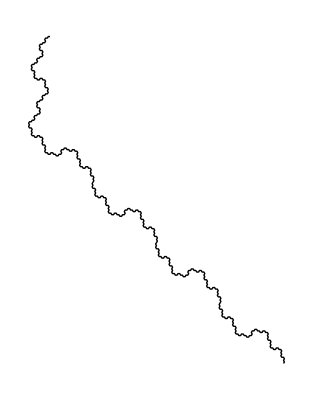

```mathematica
turtle1[4,s,"FpFmF",Pi/3.]
```

```mathematica
turtle[nit_,str_,rrule_,angolo_]:=Module[{R= Chop[RotationMatrix[angolo]],RInv=Chop[RotationMatrix[ - angolo]]},F[{x_,v_}]:= {x+v, v};
p[{x_,v_}] := {x, R.v};
m[{x_,v_}]:= {x,RInv.v};l=linee[RRule[ToLst[str],rrule,nit]];Graphics[Flatten[Table[{Hue[t/Length[l]],Line[{l[[t]],l[[t+1]]}]},{t,1,Length[l]-1}]],Background->Black,ImageSize->Large]]
```

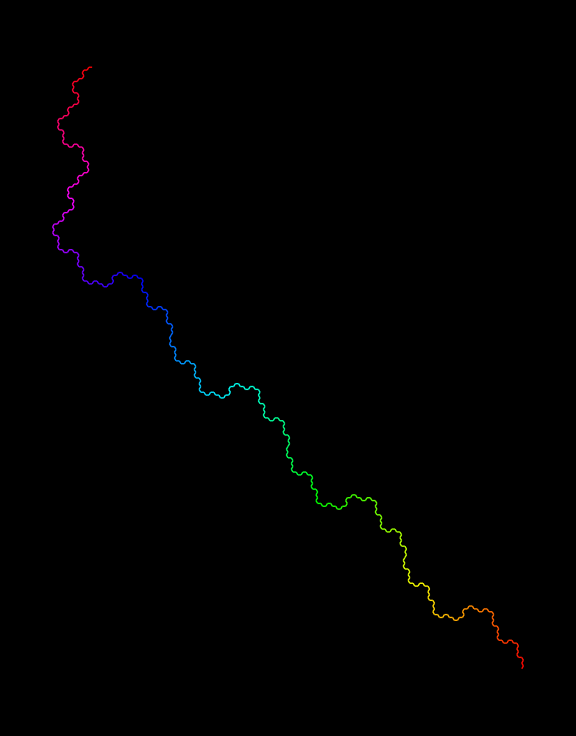

```mathematica
turtle[4,s,"FpFmF",Pi/3.]
```

L’esempio mostrato sopra parte da una stringa s casuale applicando una regola di sostituzione di F→ { F, p, F, m, F } .

Proviamo ora la funzione Turtle[.....] con rrule = “FpFmmFmmFppFppFmF” ( sostituendolo al vettore di partenza otterrei:   )  pertendo da una stringa iniziale  che rappresenta un triangolo equilatero ( utilizziamo un angolo di Pi/3 ).

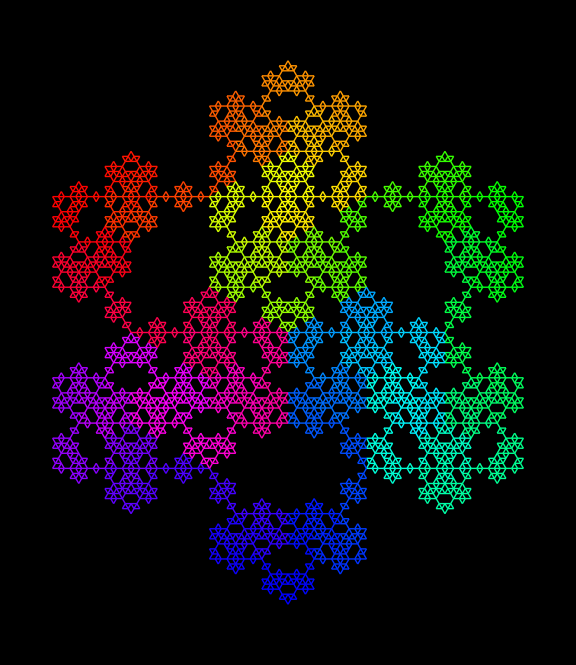

```mathematica
t=turtle[4,"FmmFmmF","FpFmmFmmFppFppFmF",Pi/3.]
```

Notiamo che la parte esterna si sovrappone allo SnowFlake per la struttura simile della rrule ( almeno nella parte esterna )
mostriamo insieme i due grafici.
Modifichiamo la turtle in modo da inserire la primitiva grafica dello SnowFlake ( che abbiamo già visto a lezione ). Non modifichiamo i colori per i singoli segmenti per rendere più chiara la lettura dell’immagine.

```mathematica
turtle2[nit_,str_,rrule_,angolo_]:=Module[{R= Chop[RotationMatrix[angolo]],RInv=Chop[RotationMatrix[ - angolo]]},F[{x_,v_}]:= {x+v, v};
p[{x_,v_}] := {x, R.v};
m[{x_,v_}]:= {x,RInv.v};Graphics[{Line[linee[RRule[ToLst[str],rrule,nit]]],Magenta,Line[linee[RRule[ToLst[str],"FpFmmFpF",nit]]]},ImageSize->Large]]
```

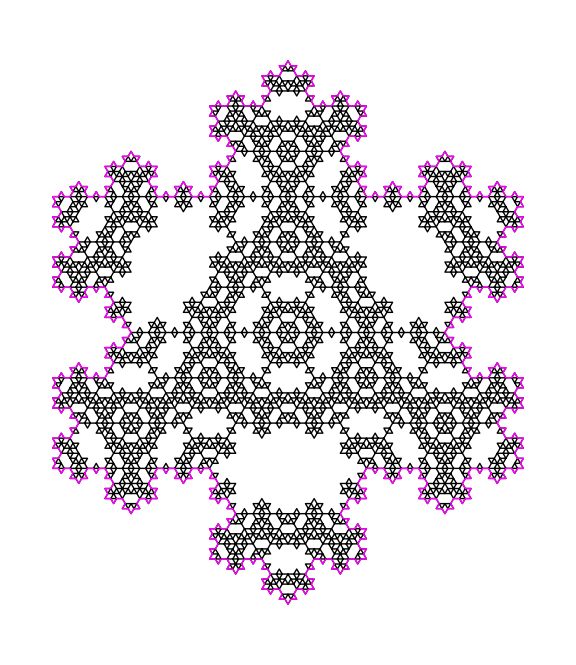

```mathematica
turtle2[4,"FmmFmmF","FpFmmFmmFppFppFmF",Pi/3.]
```

## Esercizio 3.5: Paesaggi frattali e dimensione box-counting

## Testo dell’esercizio

### Testo dell’esercizio

a) Costruire un (bel) paesaggio frattale.

b) Determinare la dimensione del “box-counting” di qualche paesaggio costruito con diversi valori dell’esponente α  del fattore di riscalamento k=2^α della variazione casuale delle altezze.

c) Si riesce a formulare un’ipotesi sulla dipendenza della dimensione box-counting dall’esponente α? [Questo è laborioso. Non è obbligatorio farlo, ma se ci riuscite è molto apprezzato]

#### Suggerimenti ed osservazioni:

Per b), evidenziate su qualche esempio che la  dimensione box-counting dipende da α.

Naturalmente la dimensione che rileverete dipenderà un po’ dal numero di iterazioni che fate nella costruzione del paesaggio frattale, come illustrato dai seguenti grafici log-log della funzione j →M_j relativi a tre diversi valori del numero di iterazioni.

Per c), confrontate i fit relativi allo stesso numero di iterazioni e due o più diversi valori di α e provate a vedere se si comprende la dipendenza da α.

## Soluzione

Soluzione del punto a)

In questo punto dobbiamo costruire un paesaggio frattale.
Cominciamo costruendo, con una procedura iterativa, una matrice quadrata di NxN numeri, che rappresentano le altezze del terreno nei punti di una griglia di NxN punti.
Si dimezza poi il passo della griglia, aggiungendo tutti i punti necessari e si assegnano le altezze nei nuovi nodi della griglia 
-  interpolando (in qualche modo, da scegliere) le altezze dei nodi vicini
- e sommando una piccola perturbazione random,  che può essere presa sia positiva che negativa. 
Si itera poi il procedimento un numero di volte opportuno, così da ottenere un bel disegno.

Cominciamo creando nuovi punti.
Prima data una lista 
                 {a , | b | ,c}
inseriamo fra ogni coppia di elementi la loro media
              {a , | (a+b)/2 , | b , | (b+c)/2 , | c}

Definiamo le seguenti due funzioni :
pmedio  calcola un vettore dove la prima coordinata rimane costante e la seconda è il punto medio tra a e b.

```mathematica
pmedio[{a_,b_}]:={a,(a+b)/2}
```

In seguito definiamo la funzione riga che crea nuovi punti della seguente forma:
1) Trasformiamo la lista {a,b,c,....}
nella lista { {a,b} , {b,c} , ..... } con un Partition che crea sottoliste di dimensione 2 e con uno spostamento di 1 (offset )

2) Mappiamo su di essa la funzione pmedio
            (a,b) →  (a,(a+b)/2).
Otteniamo così
            {{a,(a+b)/2},{b,(b+c)/2}, ....}
            
3)Ed infine appiattiamo la lista così ottenuta ( con Flatten )  e riaggiungiamo l’ultimo elemento, che è andato perso ( Append applicato all’ ultimo elemento della lista passata come parametro, usiamo il comando Last che prende l’ultimo elemento di una lista )

```mathematica
riga[lista_]:=Append[Flatten[ Map[ pmedio,Partition[lista,2,1]]], Last[lista]]
```

Per inserire nuove righe e colonne in una matrice M mappiamo la funzione riga
- prima su M (così da applicarla alle righe della matrice, cioè  inserire fra ogni coppia di elementi nella riga la loro media)
- e poi sulla trasposta della matrice così ottenuta (per applicarla alle colonne della matrice)

```mathematica
aumentare[matrice_]:=Transpose[riga/@Transpose[riga/@matrice]]
```

In ogni iterazione dobbiamo variare le altezze dei nuovi punti che aggiungiamo alla griglia. Queste altezze verrano decretate con tre parametri: r, α   e n.
All’iterazione  n=1,2,...  aggiungiamo ad ogni media un numero casuale che si incontra:
- in un intervallo simmetrico attorno allo zero (-r,r)
- e che decresce a potenza con n:  2^(- α n) con α >0 (ma in pratica, prendremo  0 < α ≤ 1/2)

Cioè scegliamo un numero random nell’intervallo  (- 2^(- α n)  r , 2^(-α n) r)  e lo aggiungiamo alla media.

Quindi adesso dobbiamo fare piccole modifiche alle funzioni definite in precedenza.
Modifichiamo la funzione pmedio definita prima:
Ridefiniamo la funzione aggiungendo i parametri r e α e sommando un numero random nell’intervallo (- 2^(- α n)  r , 2^(-α n) r) alla media

```mathematica
pmedio[{a_,b_},{r_,α_},n_]:={a,(a+b)/2 +  2^(-α n)r  RandomReal[{-1,1 }]}
```

Siccome la funzione riga definita prima ha bisogno della funzione pmedio che a sua volta ha bisogno dei parametri r e α, aggiungiamo i parametri r e α  alla funzione riga.
In più, siccome la funzione pmedio ha bisogno di essere mappata su Partition[....] ci serviamo di Map.

```mathematica
riga[lista_,{r_,α_},n_]:= Append[Flatten[Map[pmedio[#,{r,α},n]&,Partition[lista,2,1]]],Last[lista]]
```

Facciamo lo stesso con la funzione aumentare:

```mathematica
aumentare[matrice_,rα_,n_]:=Transpose[    Map[ riga[ #,rα,n]&, Transpose[ Map[ riga[ #,rα,n]& , matrice]]]  ]
```

Adesso vogliamo applicare ripetutamente la funzione   (matrice,n) → aumentare(matrice,{r,α},n),  con α e r fissati ma incrementando   n   ogni volta.
Quindi usiamo la funzione Fold[f,x,list] che dà l’elemento :   Fold[f, x, {a, b, c}] →    f[f[f[x,a],b],c]

Per rα fissato, la funzione aumentare è pensata come funzione della matrice ed n (che sono i suoi primo e terzo parametro). Quindi scriviamo   aumentare[ #1 , rα , #2 ]&.

Chiamamo a questa funzione iterazione

```mathematica
iterazione[matrice_,rα_,n_]:= Fold[    aumentare[#1,rα,#2]&,matrice,Range[n]]
```

Vogliamo ora creare la figura usando la funzione ListPlot3D.
Per ragioni esthetiche, abbiamo elliminato la box, la maglia e gli assi.

```mathematica
figura[matrice_,rα_,n_]:= ListPlot3D[ iterazione[matrice,rα,n],
                                        Mesh->False,
                                        Boxed->False,
                                        Axes->False,
                                        PlotRange->All]
```

Facciamo una prova con una matrice 4x4:

```mathematica
matrice={{1,0,1,2},{2,10,4,1},{3,0,1,0},{1,1,7,10}};
figura[matrice,{.25,.12},6]
```

-Graphics3D-

Disegnamo un lago. Per farlo dobbiamo scelgere un valore “livello del mare” e cambiando  l’altezza dei punti più bassi a questo valore.
Definiamo la funzione lago, che prende il massimo tra un’altezza h e il livello del mare, quindi mantiene le altezze dei punti che sono sopra il livello del mare e mette il valore  livellomare  a quelli valori sotto il livello del mare.

```mathematica
lago[h_,livellomare_]:=Max[h, livellomare]
```

Adesso mappiamo questa funzione rispetto alle componenti della matrice creata dalla funzione iterazione.
Osserviamo che mappiamo a livello { 2 }, perché la matrice è una lista di liste (ha  profondità due) e applichiamo la funzione lago a ogni elemento della matrice.
Chiamamo a questa funzione paesaggio:

```mathematica
paesaggio[matrice_,rα_,livellomare_,n_]  :=   Map[lago[#,livellomare]&,iterazione[matrice,rα,n] , {2} ]
```

Finalmente disegnamo questo paesaggio usando di nuovo la funzione ListPlot3D.
Per concludere l’esercizio dobbiamo coloreare il nostro paesaggio, in questo caso abbiamo usato il colore “FallColors” della funzione ColorFunction di Mathematica

```mathematica
fig[matrice_,rα_,livellomare_,n_]:=ListPlot3D[paesaggio[matrice,rα,livellomare,n],Mesh->None  , Boxed->False , Axes->False , PlotRange->All,ColorFunction->"AlpineColors"]
```

Disegnamo il nostro paesaggio, usando la matrice definita prima

```mathematica
matrice={{1,0,1,2},{2,10,4,1},{3,0,1,0},{1,1,7,10}};
im=fig[matrice,{.25,.12},2,7]
```

-Graphics3D-

Determiniamo ora la dimensione del BoxCounting al variare del parametro α, fattore di riscalamento delle altezze.

Per prima cosa costruiamo un insieme ricco di punti del paesaggio Frattale. 
Sappiamo che tali punti si ricavano dalla matrice delle altezze come abbiamo osservato precedentemente.
Utilizziamo allora la funzione paesaggio con la matrice iterazione applicata un certo numero di volte ( abbiamo scelto 7 volte poichè mi individua 148 225 punti ).
Ovviamente con un numero di iterazioni diverso potrei giungere ad una dimensione frattale differente. Scegliamo un numero abbastanza elevato per rimanere maggiormente fedeli all’approssimazione dell’algoritmo applicato infinite volte.

```mathematica
l=paesaggio[matrice,{.25,.12},2,7]
```

{1}
 |  |  |  |

```mathematica
Length[l]
```

385

Vogliamo determinare al variare del numero di cubi che ricoprono lo spazio quanti ne servano per ricoprire la figura.
Pensiamo alla figura come se fosse contenuta interamente in un cubo unitario perciò riscaliamo correttamente tutti i punti rappresentati dalle entrate della matrice e rendiamo tutte le entrate positive.
Quest’operazione ci permette di avere tutta la sua figura riscalata in ognuna delle direzioni dello spazio tridimensionale.

```mathematica
massimo=Max[Flatten[l]]
```

10.1316

```mathematica
fratt1=Flatten[Table[{m/384.,t/384.,l[[m+1]][[t+1]]/massimo}, {m,0,384},{t,0,384}],1]
```

{{0.,0.,0.197402},{0.,0.00260417,0.197402},{0.,0.00520833,0.197402},{0.,0.0078125,0.197402},{0.,0.0104167,0.197402},{0.,0.0130208,0.197402},{0.,0.015625,0.197402},{0.,0.0182292,0.197402},148210,{1.,0.984375,0.981859},{1.,0.986979,0.981627},{1.,0.989583,0.996063},{1.,0.992188,0.998363},{1.,0.994792,0.983877},{1.,0.997396,0.976785},{1.,1.,0.987011}}
 |  |  |  |

Definiamo la funzione M[ j, lista] che “distanzia” i punti di un fattore j in ogni entrata quindi potrebbero capitare in un numero di cubi di lato 1 diverso. ( E’ l’equivalente di creare ipercubi via via più piccoli di lato 1/j e contare quanti di essi contengono la i punti).
Utilizziamo Floor ( mi individua l’intero più piccolo ≥ dell’entrata della matrice ) in ognuna delle entrate con l’elemento della matrice originale opportunamente riscalato.
Eseguiamo poi Length[Union[....]] che mi permettete di non contare gli elementi uguali della lista che si è formata.

```mathematica
M[j_,lista_]:=Length[Union[Map[{Floor[j * #[[1]]],Floor[j*#[[2]]],Floor[j*#[[3]]]} &, lista]]]
```

Definiamo poi BC[ lista, n, p ] che effettua il grafico di una lista di punti in scala logaritmica di { j, M[ j, lista] } con j che va da 1 a n di passo p .

```mathematica
BC[lista_,n_,p_,col_]:=ListLogLogPlot[ Table[ {j,M[j,lista]},{j,1,n,p}],PlotStyle->col ,PlotRange->{{10,10000},{0,1.5*10^5}}]
```

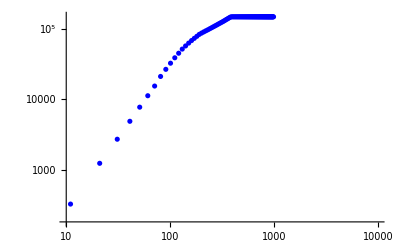

```mathematica
s1=BC[fratt1,1000,10,Blue]
```

Notiamo che il numero di cubi ad un certo punto si stabilizza più o meno al numero di punti individuati dalla matrice di partenza. Questo perchè si sono troppo distanziati i punti di partenza tanto che rientrano ognuno in un cubo diverso.
dobbiamo quindi anche diminuire n massimo per evitare che influsca nella media del grafico.

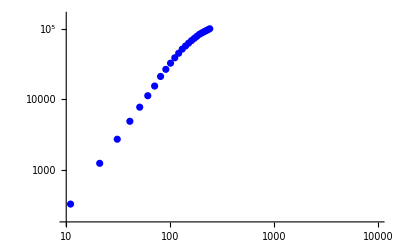

```mathematica
BC[fratt1,250,10,Blue]
```

Vogliamo trovare l’andamento medio lineare ( Fit ) in un’opportuna area di grafico definiamo quindi fit[ lista_, j1_, j2, p_ ].
Se determino questo ottengo la dimensione del Box-counting =  lim j→∞ ( log M1/j  / log j ) 
con M1/j numero di cubi di lato 1/j che contengono punti del paesaggio frattale ( qui corrispondente a M[ j, lista] )

```mathematica
fit[lista_,j1_,j2_,p_]:= Fit[ Table[{Log@j,Log@M[j,lista] },{j,j1,j2,p}] , {1,x},x]
```

```mathematica
fit[fratt1,80,130,10]
```

1.71802+1.87603 x

La dimensione del primo paesaggio frattale è quindi circa 1.87848

Mostriamo altri esempi mutando α
Proviamo α=0.5 e α= 0.7.

```mathematica
fratt2l=paesaggio[matrice,{.25,.5},2,7];
```

```mathematica
fratt3l=paesaggio[matrice,{.25,.7},2,7];
```

```mathematica
l1=Length[fratt2l];
l2=Length[fratt3l];
```

```mathematica
massimo2=Max[Flatten[fratt2l]];
massimo3=Max[Flatten[fratt3l]];
```

```mathematica
fratt2=Flatten[Table[{m/(l1-1),t/(l1-1),fratt2l[[m+1]][[t+1]]/massimo2}, {m,0,l1-1},{t,0,l1-1}],1];
fratt3=Flatten[Table[{m/(l2-1),t/(l2-1),fratt3l[[m+1]][[t+1]]/massimo3}, {m,0,l2-1},{t,0,l2-1}],1];
```

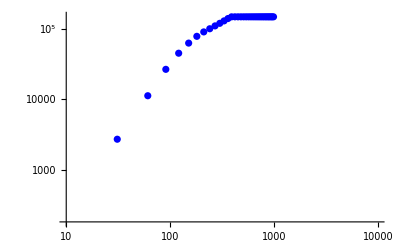

```mathematica
s1b=BC[fratt1,1000,30,Blue];
```

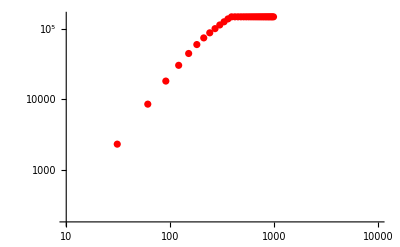

```mathematica
s2=BC[fratt2,1000,30,Red];
```

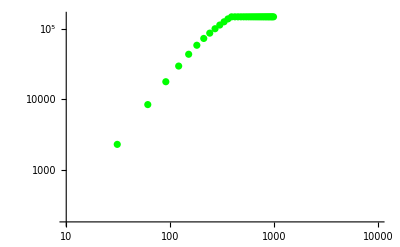

```mathematica
s3= BC[fratt3,1000,30,Green];
```

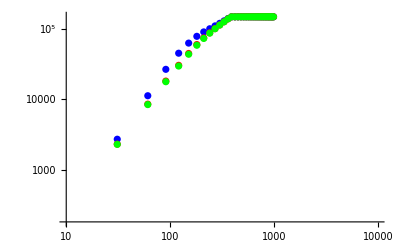

```mathematica
(*Show[s1b,s2,s3]*)
```

Notiamo che all’aumentare di α la curva si stabilisce più velocemente

```mathematica
fit[fratt2,80,150,30]
```

1.61227+1.81558 x

```mathematica
fit[fratt3,80,150,30]
```

1.67434+1.79769 x